(-2+Np) (-1+Np) Np+(-1+(1+2 Ds)^d) (-1+Np) Np^2+(-1+(1+2 Ds)^d) Np^2 (-1+(-1+(1+2 Ds)^d) Np)

(-1+Np) Np+(-1+(1+2 Ds)^d) Np^2

Cp ((-1+Np) Np+(-1+(1+2 Ds)^d) Np^2)+Ct ((-2+Np) (-1+Np) Np+(-1+(1+2 Ds)^d) (-1+Np) Np^2+(-1+(1+2 Ds)^d) Np^2 (-1+(-1+(1+2 Ds)^d) Np))

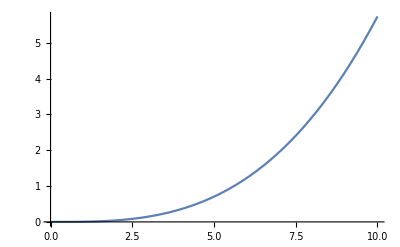

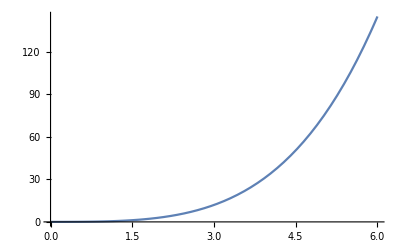

```mathematica
numberOfOtherSpace = Np*((2*Ds+1)^d-1);
numberOfTriangels = Sum[Sum[Sum[1,{k, 0, numberOfOtherSpace-2}],{j, 0, numberOfOtherSpace-1}],{i, 0, Np-1}]+Sum[Sum[Sum[1,{k, 0, numberOfOtherSpace-1}],{j, 0, Np-2}],{i, 0, Np-1}]+Sum[Sum[Sum[1,{k, 0, Np-3}],{j, 0, Np-2}],{i, 0, Np-1}]

numberOfPairs = Sum[Sum[1,{j, 0, numberOfOtherSpace-1}],{i, 0,Np-1}]+Sum[Sum[1,{j, 0, Np-2}],{i, 0,Np-1}]

totalCalculationTime = numberOfPairs*Cp + numberOfTriangels*Ct

Plot[totalCalculationTime/.{d->2,Ds->1, Cp->55*10^-6, Ct->80*10^-6}, {Np, 0, 10}]
Plot[totalCalculationTime/.{d->2,Np->4, Cp->55*10^-6, Ct->80*10^-6}, {Ds, 0, 6}]
```